## 449 HW#1

#### 1) Show that the components of the momentum operator commute: [(p̂)_x,(p̂)_y]=0.

[(p̂)_x,(p̂)_y]ψ=-ⅈ ℏ [∂_x,∂_y]ψ=-ⅈ ℏ(∂_x ∂_y -∂_y ∂_x)ψ=0

#### 2) Let p be the eigenvectors of the momentum operator, with eigenvalues ℏ k, and r the eigenvectors of the position operator. Find the position representation rp of the momentum eigenstates.

-ⅈ ℏ∇ ⅇ^(ⅈ k·r)=ℏ k ⅇ^(ⅈ k·r)→rp =ⅇ^(ⅈ k·r)

#### 3) Show that in a region of space with V(r)=const, E=(ℏ^2 k^2)/(2 m)+V are the eigenvalues of the Schrodinger equation, and p are the eigenvectors.

H=(p̂)^2/(2m)+V; [p̂,H]=0→ E=(ℏ^2 k^2)/(2 m)+V

#### 4) Snell’s law for matter waves: suppose V(r)={V_0 | z<0 V_1 | z>0. A beam of particles with momentum ℏ k_i impinges upon the plane z=0, with ẑ·k_i=k_i cos(θ_i). At z=0, the beam is partially reflected and partially transmitted. Show that the reflected beam has ẑ·k_r=- k_icos(θ_i), and find the value of ẑ·k_t=k_t cos(θ_t) for the transmitted beam.

The boundary condition at z=0 must hold for all values of x & y.  Thus ⅇ^(ⅈ k_ix x+ⅈ k_iy y)=ⅇ^(ⅈ k_rx x+ⅈ k_ry y)=ⅇ^(ⅈ k_tx x+ⅈ k_ty y).  Thus k_rx=k_ix,k_ry=k_iy, k_rz=-k_iz, with the minus sign showing that the z-component of the momentum is reversed for the reflected wave.  Likewise k_tx=k_ix. Also we have ℏ^2 k_i^2+2m V_0=ℏ^2 k_t^2+2m V_1 Hence k_i sin(θ_i)=k_t sin(θ_t)→sin(θ_t)=sin(θ_i)k_i/(√(k_i^2+(2m)/ℏ^2(V_0-V_1)))

#### 5) Fresnel coefficients for matter waves: Use boundary conditions at z=0 to find the amplitudes of the reflected and transmitted beams.

u_z=Piecewise[{{ⅇ^(ⅈ k_iz z)+A ⅇ^(-ⅈ k_iz z), z<0}, {B ⅇ^(ⅈ k_tz z), z>0}}]→ Logarithmic derivative continuous:  (∂_z (ⅇ^(ⅈ k_iz z)+A ⅇ^(-ⅈ k_iz z)))/(ⅇ^(ⅈ k_iz)+A ⅇ^(-ⅈ k_iz z))|_(z=0)=(ⅈ k_iz(1-A))/(1+A)=ⅈ k_tz

```mathematica
Solve[{(ⅈ Subscript[k, iz](1-A))/(1+A)== ⅈ Subscript[k, tz],1+A ==B},{A,B}]
```

{{A→-(-k_iz+k_tz)/(k_iz+k_tz),B→(2 k_iz)/(k_iz+k_tz)}}

#### 6) Let V_0=0, V_1=(ℏ^2 Q^2)/(2m). Plot the transmitted probability as a function of k_i, for θ_i=45^o.

let u=k_i/Q

```mathematica
Subscript[θ, t]=ArcSin[Sin[π/4] u/(√(u^2-1))];
```

```mathematica
Ptrans=1-Abs[-(-Subscript[k, iz]+Subscript[k, tz])/(Subscript[k, iz]+Subscript[k, tz])]^2//.{Subscript[k, iz]->Q u Cos[π/4],Subscript[k, t]-> Q √(u^2-1^2),Subscript[k, tz]-> Subscript[k, t] Cos[ArcSin[Sin[π/4] u/(√(u^2-1))]]}//Simplify
```

1-Abs[(u-√(-2+u^2))/(u+√(-2+u^2))]^2

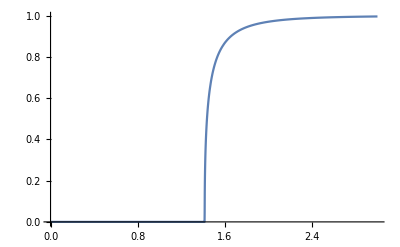

```mathematica
Plot[Ptrans//.{Subscript[k, iz]->Q u Cos[π/4],Subscript[k, t]->Q √(u^2-1^2),Subscript[k, tz]-> Subscript[k, t] Cos[ArcSin[Sin[π/4] u/(√(u^2-1))]]},{u,0,3},{PlotRange->All}]
```

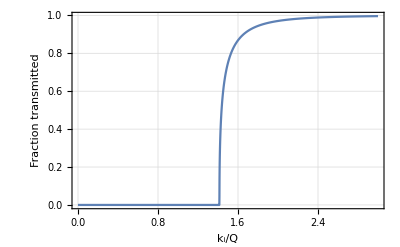

```mathematica
ThadPlot[%,{"k_i/Q","Fraction transmitted"}]
```

#### 7) Why is the beam totally reflected for Q<k<1.4 Q?

ℏ^2 k_i^2=ℏ^2 k_t^2+ℏ^2 Q^2
k_ix^2+k_iz^2=k_tx^2+k_tz^2+Q^2→k_iz^2=k^2 cos[θ_i]^2=k_tz^2+Q^2→k_tz^2=k^2 cos[θ_i]^2-Q^2

Therefore k_tz^2<0 for k<Q/cos[θ_i]=√2 Q  . The transmitted beam is exponentially damped (evanescent) for k<√2 Q.

#### 8) Suppose that in 2 dimensions the potential energy is V(x,y)=V_x(x)+V_y(y), so that H=H_x(x)+H_y(y). Calculate [H_x,H_y] and use your result to argue that the eigenstates must be of the form ψ(x,y)=ψ_x(x)ψ_y(y). Find the Schrödinger equations obeyed by ψ_x and ψ_y.

H_x=p_x^2/(2m)+V_x, H_y=p_y^2/(2m)+V_y, [H_x,H_y]=0 so the eigenstates are eigenstates of both H_x and H_y.  ψ_x ψ_y fits the bill. H_x ψ_x=E_x ψ_x,H_y ψ_y=E_y ψ_y, E=E_x+E_y.

#### 9) Find the energies and eigenstates for motion in the potential V(x,y)=Piecewise[{{1/2 κ x^2, 0<y<a}, {∞, Elsewhere}}]. Name your two quantum numbers n_x and n_y. Plot the lowest 10 energy levels for the case (m a^4 κ)/ℏ^2=π^4/4and be sure to note any degeneracies.

This is of the right form: V_x=1/2 κ x^2, V_y={0 | 0<y<a
∞ | Elsewhere.  Thus E =√(ℏ^2 κ/m)(n_x+1/2)+(ℏ^2 π^2)/(2m a^2)n_y^2=(ℏ^2 π^2)/(2m a^2)(n_y^2+√((4 a^4 m κ)/(π^4 ℏ^2))(n_x+1/2))=(ℏ^2 π^2)/(2m a^2)(n_y^2+n_x+1/2)

```mathematica
<<"http://tinyurl.com/pl27fdu"
```

```mathematica
{nxs,nys,energies}=(Table[{Subscript[n, x],Subscript[n, y],Subscript[n, y]^2+Subscript[n, x]+1/2},{Subscript[n, y],1,5},{Subscript[n, x],0,5}]~Flatten~1)ᵀ
```

{{0,1,2,3,4,5,0,1,2,3,4,5,0,1,2,3,4,5,0,1,2,3,4,5,0,1,2,3,4,5},{1,1,1,1,1,1,2,2,2,2,2,2,3,3,3,3,3,3,4,4,4,4,4,4,5,5,5,5,5,5},{3/2,5/2,7/2,9/2,11/2,13/2,9/2,11/2,13/2,15/2,17/2,19/2,19/2,21/2,23/2,25/2,27/2,29/2,33/2,35/2,37/2,39/2,41/2,43/2,51/2,53/2,55/2,57/2,59/2,61/2}}

```mathematica
in=Ordering[energies]⟦;;10⟧
```

{1,2,3,4,7,5,8,6,9,10}

here’s a list of the lowest energy levels, along with their n_x and n_y values.

```mathematica
{nxs⟦in⟧,nys⟦in⟧,energies⟦in⟧}ᵀ
```

{{0,1,3/2},{1,1,5/2},{2,1,7/2},{3,1,9/2},{0,2,9/2},{4,1,11/2},{1,2,11/2},{5,1,13/2},{2,2,13/2},{3,2,15/2}}

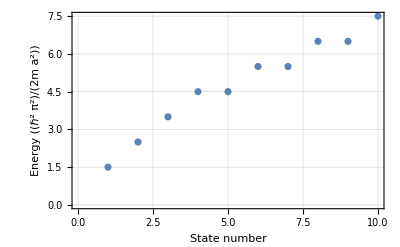

```mathematica
ThadPlot[ListPlot[energies⟦in⟧],{"State number","Energy ((ℏ^2 π^2)/(2m a^2))"}]
```